{1/2 (-σ-√(-4+σ^2)),1/2 (-σ+√(-4+σ^2))}

{{y→0,x→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{y→0,x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

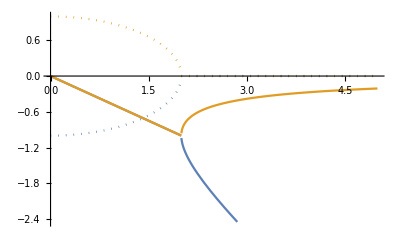

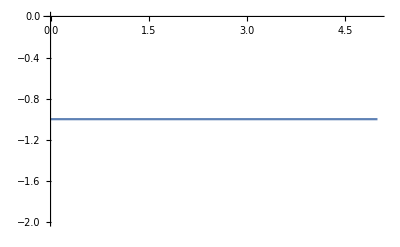

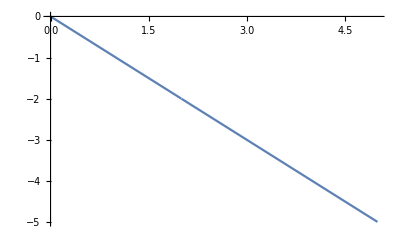

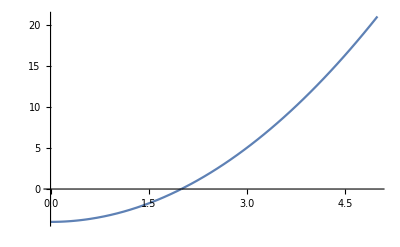

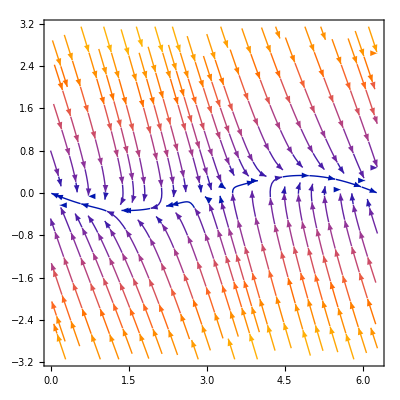

```mathematica
f[x_,y_] = y;
g[x_,y_] = -Sin[x]-σ*y;
σ = .;
J[x_,y_]:= {{0, 1}, {-Cos[x], -σ}};
eval =J[0,0] // Eigenvalues
Solve[y==0 &&-Sin[x]-3*y==0,{x,y}]
ReImPlot[{eval[[1]], eval[[2]]}, {σ,0, 5}]
Plot[Det[J[π,0]], {σ, 0,5}]
Plot[eval[[1]]+eval[[2]], {σ, 0,5}]
Plot[
(eval[[1]]+ eval[[2]])^2-4*(eval[[1]]* eval[[2]]), {σ, 0,5}]
StreamPlot[{f[x,y],g[x,y]}/.σ->3,{x,0,2*π},{y, -π,π}]
```

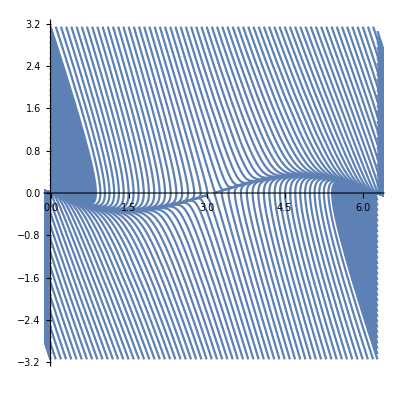

```mathematica
minx = 0; 
maxx = 2*π;
miny = -π; 
maxy = π;
σ = 3;
sol[x0_ , y0_] := NDSolve[{x'[t] ==y[t], y'[t]==-Sin[x[t]]-σ*y[t] , x[0] ==x0 , y[0] ==y0}, {x,y} , {t, 0, 10}]
initialCondition = Join[Table[{0,y},{y , miny , maxy , 0.1}] ,Table[{minx,y},{y , miny , maxy , 0.1}] , Table[{maxx,y},{y , miny , maxy, 0.1}] , Table[{x,miny},{x , minx , maxx , 0.1}] , Table[{x,maxy},{x , minx , maxx, 0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[initialCondition[[i,1]] , initialCondition[[i,2]]]], {t,0,10}, PlotRange->{{minx, maxx}, {miny,maxy}}] ,{i,Length[initialCondition]} ]]
```